# Settings

```mathematica
EigensystemSorted[H_,ρ_?NumericQ,ϕ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[H[ρ,ϕ]];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,Map[Normalize,eig]}
]
```

```mathematica
endif[H_,{x_?NumericQ,y_?NumericQ},bottomlevel_]:=Module[{e},
e=Sort@N@Eigenvalues[H[x,y]];
e[[bottomlevel+1]]-e[[bottomlevel]]]
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
(*chevron plot markers*)(*V shape: \/(lower-level DPs)*)vMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,1},{0,0},{1,1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
(* ∧shape: /\  (upper-level DPs)*)uMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,-1},{0,0},{1,-1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
plus=Graphics[{Line[{{-√2,0},{√2,0}}],Line[{{0,-√2},{0,√2}}]}];
```

```mathematica
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
ResourceFunction["PlotGrid"];
```

```mathematica
MyBlue=RGBColor[0,0.4,1];
MyGreen=RGBColor[0,1,0];
MyRed=RGBColor[1,0,0];
MyViolet=RGBColor[128/255,0,128/255];
geodColor=RGBColor[0,0.7,0.7];
geodThickness=0.015;
infGray=GrayLevel[0.3];
fillGray=GrayLevel[0.92];
blobGray=GrayLevel[0.9];
```

# Qutrit in magnetic field

```mathematica
(*Spin-1 matrices*)
Sx=1/Sqrt[2] {{0,1,0},{1,0,1},{0,1,0}};
Sy=1/Sqrt[2] {{0,-I,0},{I,0,-I},{0,I,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};

(*Full spin-1 Hamiltonian with zero-field splitting*)
(*Following NV center convention from [Rondin14]*)
```

```mathematica
HSpinFull[Bx_,By_,Bz_,D_,E_,μB_,g_]:=D*Sz.Sz+E*(Sx.Sx-Sy.Sy)+g μB(Bx*Sx+By*Sy+Bz*Sz)//Simplify
```

```mathematica
Chop@HSpinFull[Bx,By,Bz,d,e,μB,g]//MatrixForm
```

(d+Bz g μB | ((Bx-ⅈ By) g μB)/(√2) | e
((Bx+ⅈ By) g μB)/(√2) | 0 | ((Bx-ⅈ By) g μB)/(√2)
e | ((Bx+ⅈ By) g μB)/(√2) | d-Bz g μB)

```mathematica
H[Bx_,Bz_]:=HSpinFull[Bx,0,Bz,d,e,μB,g] (*multiply by 1000 to use mT as units of B*)
```

#### Exact root finding

```mathematica
ens=Eigenvalues[H[0,y]]
```

{0,d-√(e^2+g^2 y^2 μB^2),d+√(e^2+g^2 y^2 μB^2)}

```mathematica
sol=Quiet@Solve[ens[[1]]==ens[[2]],y]
root=sol[[2]]
```

{{y→-(√(d^2-e^2))/(g μB)},{y→(√(d^2-e^2))/(g μB)}}

{y→(√(d^2-e^2))/(g μB)}

```mathematica
ens/.y->0
```

{0,d-√(e^2),d+√(e^2)}

So the energy gap is 2e.

```mathematica
d=2.87;      (* GHz-zero-field splitting*)
e=0.5;            (* e~100 kHz for high purity chemical vapour deposition grown diamond samples, but we need 0 to get exact crossing*)
μB=14;    (*GHz/T-effective gyromagnetic parameter*)
g=2 ;(*Landé g-factor*)

Chop@H[Bx,Bz]//MatrixForm
endif1[y_?NumericQ]:=Module[{sp},
sp=Sort[Eigenvalues[N@H[0,y]]];
sp[[2]]-sp[[1]]
]
```

(2.87+28 Bz | 14 √2 Bx | 0.5
14 √2 Bx | 0 | 14 √2 Bx
0.5 | 14 √2 Bx | 2.87-28 Bz)

```mathematica
yroot=N[y/.root,43]
```

0.100933

```mathematica
{Bz0,Bz1,Bz2}={0,2yroot,yroot}; (*needed for shifts later*)
```

#### Plots

```mathematica
plot3d=Plot3D[Evaluate[Sort[Eigenvalues[H[Bx,Bz]]]],{Bx,-0.2,0.2},{Bz,-0.2,0.2},PlotPoints->20,AxesLabel->{"B_x","B_z","E"},
PlotStyle->{
Directive[RGBColor[0.,0.2,0.7],Opacity[0.7]],
Directive[RGBColor[0.2,0.5,0.9],Opacity[0.5]],
Directive[RGBColor[0.5,0.7,1],Opacity[0.2]]}]
```

-Graphics3D-

```mathematica
{zMin,zMax}={0,10};
colorMapping=(Blend[{White,Black},Rescale[#,{zMin,zMax}]]&);

optEndif={PlotPoints->10,ColorFunctionScaling->False,ColorFunction->colorMapping,FrameLabel->{"B_x","B_z"}};
```

Energy differences between levels

```mathematica
grid=Quiet@ResourceFunction["PlotGrid"][{{Show[{
DensityPlot[endif[H,{Bx,Bz},2],{Bx,-0.23,0.23},{Bz,-0.23,0.23},Evaluate@optEndif] (*top plot*)
}]},
{Show[{DensityPlot[endif[H,{Bx,Bz},1],{Bx,-0.23,0.23},{Bz,-0.23,0.23},Evaluate@optEndif],(*bottom plot background*)
ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{cross,0.1}],  (*DP1*)
ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{cross,0.1}] (*DP0*)
}]}}]
```

-Graphics-

```mathematica
Sort@Eigenvalues[H[0,Bz0]]
Sort@Eigenvalues[H[0,Bz2]]
Sort@Eigenvalues[H[0,-Bz2]]
```

{0.,2.37,3.37}

{0.,9.94817×10^-17,5.74}

{0.,9.94817×10^-17,5.74}

## Analysis

```mathematica
xyTorϕ={x->r Cos[ϕ],y->r Sin[ϕ]};
H0[r_,ϕ_]=H[x,y]/.{y->y-Bz2}/.xyTorϕ//FullSimplify;(* around dp on M0*)
H1[r_,ϕ_]=H[x,y]/.{y->y+Bz2}/.xyTorϕ//FullSimplify; (* around dp on M0*)
H2[r_,ϕ_]=H[x,y]/.xyTorϕ//FullSimplify; (* around dp on M1*)
```

```mathematica
(*check the r->0 degeneracy*)
Chop@Sort@Eigenvalues@H0[0,ϕ]
Chop@Sort@Eigenvalues@H1[0,ϕ]
Chop@Sort@Eigenvalues@H2[0,ϕ]
```

{0,0,5.74}

{0,0,5.74}

{0,2.37,3.37}

```mathematica
(*conversion from radial to shifted radial, which will be used mainly for geometry*)
r[R_]:=RealSign[R-1/2](R-1/(4R))
ϕ[R_,Φ_]:=UnitStep[R-1/2]Φ+UnitStep[1/2-R](Φ+π)
HASR[H_,R_,Φ_]:=H[r[R],ϕ[R,Φ]]//FullSimplify
```

```mathematica
(*Hamiltonian in three different shifted radial coordinates, around three different DPs*)
HS0[R_?NumericQ,Φ_?NumericQ]:=HASR[H0,R,Φ];
HS1[R_?NumericQ,Φ_?NumericQ]:=HASR[H1,R,Φ];
HS2[R_?NumericQ,Φ_?NumericQ]:=HASR[H2,R,Φ];
```

```mathematica
SRToR[{R_,Φ_}]:={r[R],Mod[ϕ[R,Φ],2π]}(*shifted radial to radial*)
RToSRIn[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (-r+√(1+r^2));
Φ=Mod[ϕ-π,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
RToSROut[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (r+√(1+r^2));
Φ=Mod[ϕ,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
SCToSR[X_,Y_]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
CToR[x_,y_]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)
RToC[r_,φ_]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
(*vector versions*)
SCToSR[{X_,Y_}]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
SRToSC[{R_,Φ_}]:={R Cos[Φ],R Sin[Φ]}; (*shifted radial to shifted cartesian*)
RToC[{r_,φ_}]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
CToR[{x_,y_}]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)

C0ToC1[{x_,y_}]:={x,y-Bz1}
C1ToC0[{x_,y_}]:={x,y+Bz1}
C0ToC2[{x_,y_}]:={x,y-Bz2}
C2ToC0[{x_,y_}]:={x,y+Bz2}
C1ToC2[{x_,y_}]:={x,y+Bz2}
C2ToC1[{x_,y_}]:={x,y-Bz2}
```

## Metric definition

```mathematica
DH1S0[R_?NumericQ,Φ_?NumericQ]=D[HASR[H0,R,Φ],R]//FullSimplify;
DH2S0[R_?NumericQ,Φ_?NumericQ]=D[HASR[H0,R,Φ],Φ]//FullSimplify;
DH1S1[R_?NumericQ,Φ_?NumericQ]=D[HASR[H1,R,Φ],R]//FullSimplify;
DH2S1[R_?NumericQ,Φ_?NumericQ]=D[HASR[H1,R,Φ],Φ]//FullSimplify;
DH1S2[R_?NumericQ,Φ_?NumericQ]=D[HASR[H2,R,Φ],R]//FullSimplify;
DH2S2[R_?NumericQ,Φ_?NumericQ]=D[HASR[H2,R,Φ],Φ]//FullSimplify;
```

```mathematica
gSLevel[hamInt_?IntegerQ,n_?IntegerQ,{λ_?NumericQ,χ_?NumericQ}]:=Module[{DH1,DH2,H,dim,dh1c,dh2c,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22,levels},
(*labeled as n=1,2,3 states*)
dim=3;
(*choose H nad derivatives*)
{H,DH1,DH2}=Which[hamInt==0,{HS0,DH1S0,DH2S0},
hamInt==1,{HS1,DH1S1,DH2S1},
hamInt==2,{HS2,DH1S2,DH2S2}];
levels=DeleteCases[Range[3],n];
{en,eig}=EigensystemSorted[H,λ,χ];
dh1c=DH1[λ,χ];
dh2c=DH2[λ,χ];

M1=Conjugate[eig⟦n⟧].dh1c.eig⟦#⟧&/@levels;
M1T=Conjugate[eig⟦#⟧].dh1c.eig⟦n⟧&/@levels;
M2=Conjugate[eig⟦n⟧].dh2c.eig⟦#⟧&/@levels;
M2T=Conjugate[eig⟦#⟧].dh2c.eig⟦n⟧&/@levels;
endif=(en⟦n⟧-en⟦#⟧)^2&/@levels;

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gS[hNum_?IntegerQ,levelOut_,levelIn_,{R_?NumericQ,Φ_?NumericQ}]:=Module[{l1,l2},
(*hNum is 0,1,2, chooses the DP, levelIn is for R<1/2, levelOut for R>1/2*)
Which[0<R<1/2,gSLevel[hNum,levelIn,{R,Φ}],R>1/2,gSLevel[hNum,levelOut,{R,Φ}],R==1/2,(gSLevel[hNum,levelOut,{1/2+10^-5,1}]+gSLevel[hNum,levelIn,{1/2-10^-5,1}])/2]
]
```

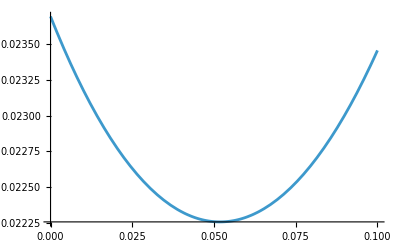

```mathematica
Plot[Det@gS[0,1,2,{R,1.}],{R,0,0.1},PlotRange->All]
```

### Plotting functions for Cartesian

```mathematica
DH1C[x_,y_]=D[H[x,y],x]//Simplify
DH2C[x_,y_]=D[H[x,y],y]//Simplify
```

{{0,14 √2,0},{14 √2,0,14 √2},{0,14 √2,0}}

{{28,0,0},{0,0,0},{0,0,-28}}

```mathematica
gC[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{dim,dh1c,dh2c,enNonSort,eigNonSort,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22,levels},
(*labeled as n=1,2,3 states*)
dim=3;
levels=DeleteCases[Range[3],n];
{enNonSort,eigNonSort}=Eigensystem[H[λ,χ]];
eigNonSort=Map[Normalize,eigNonSort];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
dh1c=DH1C[λ,χ];
dh2c=DH2C[λ,χ];

M1=Conjugate[eig⟦n⟧].dh1c.eig⟦#⟧&/@levels;
M1T=Conjugate[eig⟦#⟧].dh1c.eig⟦n⟧&/@levels;
M2=Conjugate[eig⟦n⟧].dh2c.eig⟦#⟧&/@levels;
M2T=Conjugate[eig⟦#⟧].dh2c.eig⟦n⟧&/@levels;
endif=(en⟦n⟧-en⟦#⟧)^2&/@levels;

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
markersize=0.1;
bgDP0Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{uMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{uMarker,markersize}]]
bgDP1Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{vMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{vMarker,markersize}]]
bgDP2Cart:=Show[ListPlot[{{0,0}},PlotStyle->MyGreen,PlotMarkers->{plus,markersize}]]
```

## Ricci scalar

```mathematica
R1[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumeric[n,λ,χ];
dg1=ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ,derTerms_?NumericQ,scale_?NumericQ]:=Module[{g,l,c,dg1,dg2,R12},
g=gNumeric[n,λ,χ];
dg1=ND[gNumeric[n,l,χ],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum];
dg2=ND[gNumeric[n,λ,c],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum];
1/(√(Abs@Det[g]))(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,derTermsIn,scale,g,dist,isClose1,isClose2,isClose3,isClose4},
(*Guttierez formula*)
derTerms=4;
derTermsIn=4;
dist=Min[Norm[{λ,χ}-#]&/@diabolicPoints[n]];
isClose1=dist<0.2;
isClose2=dist<0.3;
isClose3=dist<0.5;

scale=Which[isClose1,0.0001,isClose2,0.0002,isClose3,0.006,True,0.03];
g=gNumeric[n,λ,χ];
1/(√(Abs@Det@g))(ND[R1[n,l,χ,derTermsIn,scale],l,λ,Terms->derTerms,Scale->scale,Method->EulerSum]+ND[R2[n,λ,c,derTermsIn,scale],c,χ,Terms->derTerms,Scale->scale,Method->EulerSum])
]
```

# Old

```mathematica
(*Step size for finite differences*)
hFD=10^-5;

(*1st and 2nd Derivatives using explicit symmetric finite differences*)
d1[f_,{x_,y_},{dx_,dy_}]:=(f[x+dx*hFD,y+dy*hFD]-f[x-dx*hFD,y-dy*hFD])/(2*hFD);

d2[f_,{x_,y_},{dx_,dy_}]:=(f[x+dx*hFD,y+dy*hFD]-2*f[x,y]+f[x-dx*hFD,y-dy*hFD])/(hFD^2);

d12[f_,{x_,y_}]:=(f[x+hFD,y+hFD]-f[x+hFD,y-hFD]-f[x-hFD,y+hFD]+f[x-hFD,y-hFD])/(4*hFD^2);

(*Brioschi Formula for Gaussian Curvature K gFunc must be a function taking {u,v} and returning a 2x2 matrix.*)
GaussianCurvatureK[gFunc_,u_?NumericQ,v_?NumericQ]:=Module[{g11,g12,g22,gMat,detG,gR,gPhi,gRR,gPhiPhi,gRPhi},(*Component wrappers for finite difference evaluation*)g11[x_,y_]:=gFunc[x,y][[1,1]];
g12[x_,y_]:=gFunc[x,y][[1,2]];
g22[x_,y_]:=gFunc[x,y][[2,2]];
gMat=gFunc[u,v];
detG=Det[gMat];
(*Prevent division by zero far from DPs where metric might be flat*)If[Abs[detG]<10^-16,Return[0.]];
(*Evaluate derivatives at {u,v}*)gR={{d1[g11,{u,v},{1,0}],d1[g12,{u,v},{1,0}]},{d1[g12,{u,v},{1,0}],d1[g22,{u,v},{1,0}]}};
gPhi={{d1[g11,{u,v},{0,1}],d1[g12,{u,v},{0,1}]},{d1[g12,{u,v},{0,1}],d1[g22,{u,v},{0,1}]}};
gRR={{d2[g11,{u,v},{1,0}],d2[g12,{u,v},{1,0}]},{d2[g12,{u,v},{1,0}],d2[g22,{u,v},{1,0}]}};
gPhiPhi={{d2[g11,{u,v},{0,1}],d2[g12,{u,v},{0,1}]},{d2[g12,{u,v},{0,1}],d2[g22,{u,v},{0,1}]}};
gRPhi={{d12[g11,{u,v}],d12[g12,{u,v}]},{d12[g12,{u,v}],d12[g22,{u,v}]}};
(1/detG^2)*(Det[{{-1/2 gPhiPhi[[1,1]]+gRPhi[[1,2]]-1/2 gRR[[2,2]],1/2 gR[[1,1]],gR[[1,2]]-1/2 gPhi[[1,1]]},{gPhi[[1,2]]-1/2 gR[[2,2]],gMat[[1,1]],gMat[[1,2]]},{1/2 gPhi[[2,2]],gMat[[1,2]],gMat[[2,2]]}}]-Det[{{0,1/2 gPhi[[1,1]],1/2 gR[[2,2]]},{1/2 gPhi[[1,1]],gMat[[1,1]],gMat[[1,2]]},{1/2 gR[[2,2]],gMat[[1,2]],gMat[[2,2]]}}])
]
(*Invariant Area Element:K*Sqrt[det g]*)
CurvatureIntegrand[gFunc_,u_?NumericQ,v_?NumericQ]:=GaussianCurvatureK[gFunc,u,v]*Sqrt[Abs[Det[gFunc[u,v]]]];
```

## 2-level

```mathematica
sx={{0,1},{1,0}};
sz={{1,0},{0,-1}};

(*Hamiltonian in Polar Coordinates*)
H2LPolar[r_,phi_]:=(r*Cos[phi])*sx+(r*Sin[phi])*sz;

(*Analytical derivatives of Hamiltonian*)
DH2Lr[r_,phi_]=D[H2LPolar[r,phi],r];
DH2Lphi[r_,phi_]=D[H2LPolar[r,phi],phi];

(*Metric calculation for the lowest band (n=1)*)
g2L[r_?NumericQ,phi_?NumericQ]:=Module[{dim=2,enNonSort,eigNonSort,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22},{enNonSort,eigNonSort}=Eigensystem[H2LPolar[r,phi]];
eigNonSort=Map[Normalize,eigNonSort];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
(*Matrix elements connecting band 1 to band 2*)M1=Conjugate[eig[[1]]].DH2Lr[r,phi].eig[[2]];
M1T=Conjugate[eig[[2]]].DH2Lr[r,phi].eig[[1]];
M2=Conjugate[eig[[1]]].DH2Lphi[r,phi].eig[[2]];
M2T=Conjugate[eig[[2]]].DH2Lphi[r,phi].eig[[1]];
endif=(en[[1]]-en[[2]])^2;
g11=Re[(M1*M1T)/endif];
g12=Re[(M1*M2T)/endif];
g22=Re[(M2*M2T)/endif];
{{g11,g12},{g12,g22}}]

(*Integrate over a disk of radius rTarget=0.03*)
rTarget2L=0.03;

Print["Integrating 2-level system..."];
int2L=NIntegrate[CurvatureIntegrand[g2L,r,phi],{r,10^-4,rTarget2L},{phi,0,2 Pi},Method->"LocalAdaptive",MaxRecursion->10];

Print["Topological phase for 2-Level patch (should be roughly -Pi/2 or -1.57): ",int2L];
```

Integrating 2-level system...

Topological phase for 2-Level patch (should be roughly -Pi/2 or -1.57): 0.

This should be 0, as the metric is degenerate.

## Test

```mathematica
(* =================================================================*)(*VALIDATION TEST:UNIT SPHERE*)(* =================================================================*)(*Metric for a unit sphere:ds^2=dθ^2+Sin[θ]^2 dϕ^2*)gSphere[θ_?NumericQ,ϕ_?NumericQ]:={{1,0},{0,Sin[θ]^2}};

Print["Testing integration on a Unit Sphere..."];
(*We integrate slightly away from the poles (0 and Pi) to avoid coordinate singularities*)
sphereInt=FastGridIntegrate[CurvatureIntegrand[gSphere,#1,#2]&,{θ,10^-4,Pi-10^-4,100},{ϕ,0,2 Pi,100}];

Print["Sphere Integrated Curvature (Expected 4π ≈ 12.5664): ",sphereInt];
```

Testing integration on a Unit Sphere...

Sphere Integrated Curvature (Expected 4π ≈ 12.5664): 12.5669

## 3-level NV centers

```mathematica
gSWrapped[R_?NumericQ,Phi_?NumericQ]:=gS[0,1,2,{R,Phi}];

rTarget3L=0.03;
Rin=1/2*(-rTarget3L+Sqrt[1+rTarget3L^2]);
Rout=1/2*(rTarget3L+Sqrt[1+rTarget3L^2]);

Print["Integration domain for R: [",Rin,", ",Rout,"] with horizon at 1/2"];
Print["Integrating 3-level Inner Manifold..."];

int3LIn=NIntegrate[CurvatureIntegrand[gSWrapped,R,Phi],{R,Rin,1/2-10^-6},{Phi,0,2 Pi},Method->"LocalAdaptive",MaxRecursion->12];

Print["Integrating 3-level Outer Manifold..."];

int3LOut=NIntegrate[CurvatureIntegrand[gSWrapped,R,Phi],{R,1/2+10^-6,Rout},{Phi,0,2 Pi},Method->"LocalAdaptive",MaxRecursion->12];

Print["Inner Manifold Contribution: ",int3LIn];
Print["Outer Manifold Contribution: ",int3LOut];
Print["Total Patch Curvature Integral: ",int3LIn+int3LOut];
```

Integration domain for R: [0.485225, 0.515225] with horizon at 1/2

Integrating 3-level Inner Manifold...

$Aborted

Integrating 3-level Outer Manifold...

$Aborted

Inner Manifold Contribution: int3LIn

Outer Manifold Contribution: int3LOut

Total Patch Curvature Integral: int3LIn+int3LOut

## Faster implementation

```mathematica
(* =================================================================*)(*FAST APPROXIMATE 2D INTEGRATOR (Midpoint Rule)*)(* =================================================================*)FastGridIntegrate[integrand_,{xVar_,xMin_,xMax_,nX_},{yVar_,yMin_,yMax_,nY_}]:=Module[{dx,dy,sum=0.,xVal,yVal},dx=(xMax-xMin)/nX;
dy=(yMax-yMin)/nY;
(*Sum over cell midpoints to avoid boundary singularities*)sum=Sum[xVal=xMin+(i-0.5)*dx;
yVal=yMin+(j-0.5)*dy;
integrand[xVal,yVal],{i,1,nX},{j,1,nY}];
sum*dx*dy];

(* =================================================================*)
(*3-LEVEL SYSTEM APPLICATION (Fast Version)*)
(* =================================================================*)

gSWrapped[R_?NumericQ,Phi_?NumericQ]:=gS[0,1,2,{R,Phi}];

rTarget3L=0.03;
Rin=1/2*(-rTarget3L+Sqrt[1+rTarget3L^2]);
Rout=1/2*(rTarget3L+Sqrt[1+rTarget3L^2]);

(*Grid Resolution:Increase these numbers for higher accuracy,decrease for faster runtime.{30,30} means 900 evaluations total per patch,which takes just seconds.*)
nR=40;
nPhi=40;

Print["Integration domain for R: [",Rin,", ",Rout,"] with horizon at 1/2"];

Print["Integrating 3-level Inner Manifold (Approximate)..."];
int3LInFast=FastGridIntegrate[CurvatureIntegrand[gSWrapped,#1,#2]&,{R,Rin,1/2,nR},{Phi,0,2 Pi,nPhi}];

Print["Integrating 3-level Outer Manifold (Approximate)..."];
int3LOutFast=FastGridIntegrate[CurvatureIntegrand[gSWrapped,#1,#2]&,{R,1/2,Rout,nR},{Phi,0,2 Pi,nPhi}];

Print["Inner Manifold Contribution: ",int3LInFast];
Print["Outer Manifold Contribution: ",int3LOutFast];
Print["Total Patch Curvature Integral: ",int3LInFast+int3LOutFast];
```

Integration domain for R: [0.485225, 0.515225] with horizon at 1/2

Integrating 3-level Inner Manifold (Approximate)...

Integrating 3-level Outer Manifold (Approximate)...

Inner Manifold Contribution: 0.167518

Outer Manifold Contribution: 0.146456

Total Patch Curvature Integral: 0.313974

# New

```mathematica
(*Bz2=N[Sqrt[d^2-e^2]/(g μB)];*)

dpList:={{0.,-Bz2},{0.,Bz2}};
```

```mathematica
gCart[level_,bx_,bz_]:=Module[{m},
m=Quiet@Check[gC[level,N[bx],N[bz]],$Failed];
If[m===$Failed||!MatrixQ[m,NumericQ],$Failed,N[(m+Transpose[m])/2]]
]
```

```mathematica
d1u4[f_,u_,v_,h_]:=(-f[u+2 h,v]+8 f[u+h,v]-8 f[u-h,v]+f[u-2 h,v])/(12 h);
d1v4[f_,u_,v_,h_]:=(-f[u,v+2 h]+8 f[u,v+h]-8 f[u,v-h]+f[u,v-2 h])/(12 h);
```

```mathematica
GaussianCurvatureGuttierez[metric_,{u_,v_},h_:3.*^-4]:=Module[{E11,F12,G22,detgAbs,R1,R2,det0,ricci},E11[uu_,vv_]:=metric[uu,vv][[1,1]];
F12[uu_,vv_]:=metric[uu,vv][[1,2]];
G22[uu_,vv_]:=metric[uu,vv][[2,2]];
detgAbs[uu_,vv_]:=Abs[E11[uu,vv] G22[uu,vv]-F12[uu,vv]^2];
R1[uu_,vv_]:=1/Sqrt[detgAbs[uu,vv]]*((F12[uu,vv]/E11[uu,vv]) d1v4[E11,uu,vv,h]-d1u4[G22,uu,vv,h]);
R2[uu_,vv_]:=1/Sqrt[detgAbs[uu,vv]]*(2 d1u4[F12,uu,vv,h]-d1v4[E11,uu,vv,h]-(F12[uu,vv]/E11[uu,vv]) d1u4[E11,uu,vv,h]);
det0=detgAbs[u,v];
ricci=1/Sqrt[det0]*(d1u4[R1,u,v,h]+d1v4[R2,u,v,h]);
ricci/2];

ChristoffelFD4[metric_,{u_,v_},h_:5.*^-4]:=Module[{dg1,dg2,dg,g0,ginv,Gamma},dg1=d1u4[metric,u,v,h];
dg2=d1v4[metric,u,v,h];
If[!MatrixQ[dg1,NumericQ]||!MatrixQ[dg2,NumericQ],Return[$Failed]];
dg={dg1,dg2};
g0=metric[u,v];
If[g0===$Failed||!MatrixQ[g0,NumericQ],Return[$Failed]];
ginv=Quiet@Check[Inverse[g0],$Failed];
If[ginv===$Failed||!MatrixQ[ginv,NumericQ],Return[$Failed]];
Gamma=Table[1/2 Sum[ginv[[rho,sigma]]*(dg[[mu]][[sigma,nu]]+dg[[nu]][[sigma,mu]]-dg[[sigma]][[mu,nu]]),{sigma,1,2}],{rho,1,2},{mu,1,2},{nu,1,2}];
{Gamma[[1]],Gamma[[2]]}];

Eps01[v_,a_]:=v[[1]] a[[2]]-v[[2]] a[[1]];
```

```mathematica
KgDsIntegralParametric[metric_,gamma_,gammaDot_,gammaDDot_,{t0_,t1_},nSamples_:1400,hConn_:5.*^-4,detgMin_:1.*^-14]:=Module[{dt,acc=0.,nBad=0,t,q,vel,acc0,gmat,detg,Gamma,Gamma1,Gamma2,covAcc,vel2,nS},nS=Round[nSamples];
dt=N[(t1-t0)/nS];
Do[t=t0+(k+0.5) dt;
q=gamma[t];
vel=gammaDot[t];
acc0=gammaDDot[t];
gmat=Quiet@Check[metric[q[[1]],q[[2]]],$Failed];
If[gmat===$Failed||!MatrixQ[gmat,NumericQ],nBad++;Continue[];];
detg=Re@Quiet@Check[Det[gmat],$Failed];
If[detg===$Failed||!NumericQ[detg]||detg<=detgMin,nBad++;Continue[];];
Gamma=Quiet@Check[ChristoffelFD4[metric,q,hConn],$Failed];
If[Gamma===$Failed||!ListQ[Gamma]||Length[Gamma]!=2||!MatrixQ[Gamma[[1]],NumericQ]||!MatrixQ[Gamma[[2]],NumericQ],nBad++;Continue[];];
{Gamma1,Gamma2}=Gamma;
covAcc=acc0+{vel.Gamma1.vel,vel.Gamma2.vel};
vel2=Re@Quiet@Check[vel.gmat.vel,$Failed];
If[vel2===$Failed||!NumericQ[vel2]||vel2<=0,nBad++;Continue[];];
acc+=Sqrt[detg]*Eps01[vel,covAcc]/vel2*dt;,{k,0,nS-1}];
{acc,<|"bad"->nBad|>}];
```

```mathematica
(*------------------------------------------------------------Boundary integral on a Cartesian circle------------------------------------------------------------*)
KgDsCircleCartesian[level_,center:{cx_,cz_},radius_,cw_:False,nSamples_:1400,hConn_:5.*^-4,detgMin_:1.*^-14]:=Module[{metric,t1,gamma,gammaDot,gammaDDot},metric=Function[{x,z},gCart[level,N[x],N[z]]];
t1=If[TrueQ[cw],-2. Pi,2. Pi];
gamma[t_]:={cx+radius Cos[t],cz+radius Sin[t]};
gammaDot[t_]:={-radius Sin[t],radius Cos[t]};
gammaDDot[t_]:={-radius Cos[t],-radius Sin[t]};
KgDsIntegralParametric[metric,gamma,gammaDot,gammaDDot,{0.,t1},nSamples,hConn,detgMin]];

(*------------------------------------------------------------Area integral int K sqrt(det g) d^2x on disk|B| <=Rmax------------------------------------------------------------*)
CurvatureIntegralDiskCartesianMidpoint[level_,Rmax_,dps_List,dpHoleRadius_,Nr_:22,Nphi_:72,detgMin_:1.*^-14,hCurv_:3.*^-4]:=Module[{metric,dr,dphi,integral=0.,nEval=0,nSkip=0,r,phi,bx,bz,gmat,detg,K,nR,nP},nR=Round[Nr];nP=Round[Nphi];
metric=Function[{x,z},gCart[level,N[x],N[z]]];
dr=N[Rmax/nR];
dphi=N[2 Pi/nP];
Do[r=(i+0.5) dr;
Do[phi=(j+0.5) dphi;
bx=r Cos[phi];
bz=r Sin[phi];
If[Min[Norm[{bx,bz}-#]&/@dps]<dpHoleRadius,nSkip++;Continue[];];
gmat=Quiet@Check[metric[bx,bz],$Failed];
If[gmat===$Failed||!MatrixQ[gmat,NumericQ],nSkip++;Continue[];];
detg=Re@Quiet@Check[Det[gmat],$Failed];
If[detg===$Failed||!NumericQ[detg]||detg<=detgMin,nSkip++;Continue[];];
K=Quiet@Check[GaussianCurvatureGuttierez[metric,{bx,bz},hCurv],Indeterminate];
If[!NumericQ[K]||K===Indeterminate,nSkip++;Continue[];];
integral+=K*Sqrt[detg]*r*dr*dphi;
nEval++;,{j,0,nP-1}];,{i,0,nR-1}];
{integral,<|"evaluated"->nEval,"skipped"->nSkip|>}];
```

```mathematica
(*-------------------------DP sheet convention-------------------------------------------*)
DPLevelOutIn[dp:{_?NumericQ,_?NumericQ}]:=If[dp[[2]]<0,{2,1},{1,2}];

(*------------------------Euler characteristic expected from the CSM construction-------------------------------------------*)
CSMEulerCharacteristic[m_Integer,dpsPerLevel_List]:=Module[{genus,b},genus=-m+Total[dpsPerLevel];
b=m+1;
2-2 genus-b];

(*------------------------------------Full Gauss-Bonnet estimate------------------------------------*)
GaussBonnetChiCSMCartesianCutoffs[Rmax_:0.3,dpHoleRadius_:0.06,Nr_:22,Nphi_:72,nBdry_:1400,hCurv_:3.*^-4,hConn_:5.*^-4,detgMin_:1.*^-14]:=Module[{levels={1,2},dps=dpList,areaTerms=Association[],outerTerms=Association[],holeTerms,areaTotal,outerTotal,holeTotal,chi},Do[areaTerms[level]=CurvatureIntegralDiskCartesianMidpoint[level,Rmax,dps,dpHoleRadius,Nr,Nphi,detgMin,hCurv];
outerTerms[level]=KgDsCircleCartesian[level,{0.,0.},Rmax,False,nBdry,hConn,detgMin];,{level,levels}];
holeTerms=Table[Module[{pair,outRes,inRes,Iout,infoOut,Iin,infoIn},pair=DPLevelOutIn[dp];
outRes=KgDsCircleCartesian[pair[[1]],dp,dpHoleRadius,True,nBdry,hConn,detgMin];
inRes=KgDsCircleCartesian[pair[[2]],dp,dpHoleRadius,True,nBdry,hConn,detgMin];
If[!MatchQ[outRes,{_?NumericQ,_Association}],<|"dp"->dp,"levels"->pair,"integral"->Indeterminate,"bad"->"outer sheet boundary failed","raw"->outRes|>,If[!MatchQ[inRes,{_?NumericQ,_Association}],<|"dp"->dp,"levels"->pair,"integral"->Indeterminate,"bad"->"inner sheet boundary failed","raw"->inRes|>,{Iout,infoOut}=outRes;
{Iin,infoIn}=inRes;
<|"dp"->dp,"levels"->pair,"integral"->Iout+Iin,"bad"->infoOut["bad"]+infoIn["bad"]|>]]],{dp,dps}];
areaTotal=Total[(areaTerms[#][[1]]&)/@levels];
outerTotal=Total[(outerTerms[#][[1]]&)/@levels];
If[!VectorQ[holeTerms[[All,"integral"]],NumericQ],Return[{Indeterminate,<|"area_2pi"->areaTotal/(2 Pi),"outer_2pi"->outerTotal/(2 Pi),"holes_2pi"->Indeterminate,"area_terms"->areaTerms,"outer_terms"->outerTerms,"hole_terms"->holeTerms,"error"->"At least one DP-hole boundary integral failed."|>}]];
holeTotal=Total[holeTerms[[All,"integral"]]];
chi=(areaTotal+outerTotal+holeTotal)/(2 Pi);
{chi,<|"area_2pi"->areaTotal/(2 Pi),"outer_2pi"->outerTotal/(2 Pi),"holes_2pi"->holeTotal/(2 Pi),"area_terms"->areaTerms,"outer_terms"->outerTerms,"hole_terms"->holeTerms|>}];
```

```mathematica
testBoundary=KgDsCircleCartesian[2,{0.,-Bz2},0.06,True,20,5.*^-4,1.*^-14];
{Head[testBoundary],testBoundary}
```

{List,{-0.0488429,<|bad→0|>}}

```mathematica
chiAnalytical=CSMEulerCharacteristic[1,{2}];

{chiGB,info}=GaussBonnetChiCSMCartesianCutoffs[0.3,0.06,22,72,1400,3.*^-4,5.*^-4,1.*^-14];
```

```mathematica
Print["Gauss-Bonnet chi estimate: ",N[chiGB,8],"   analytic: ",chiAnalytical];
Print["Breakdown divided by 2 Pi: area = ",N[info["area_2pi"],8],", outer = ",N[info["outer_2pi"],8],", holes = ",N[info["holes_2pi"],8]];
Print["DP hole boundaries, out+in per DP:"];
Do[Print["  dp = ",info["hole_terms"][[k,"dp"]],"  levels = ",info["hole_terms"][[k,"levels"]],"  I/(2 Pi) = ",N[info["hole_terms"][[k,"integral"]]/(2 Pi),8],"  bad = ",info["hole_terms"][[k,"bad"]]],{k,Length[info["hole_terms"]]}];
```

Gauss-Bonnet chi estimate: -2.01492   analytic: -2

Breakdown divided by 2 Pi: area = -0.899375, outer = -0.920403, holes = -0.195145

DP hole boundaries, out+in per DP:

dp = {0.,-0.100933}  levels = {2,1}  I/(2 Pi) = -0.0975723  bad = 0

dp = {0.,0.100933}  levels = {1,2}  I/(2 Pi) = -0.0975723  bad = 0